```mathematica
minx=-π-0.5;  maxx=π+0.5; miny=-2.5; maxy=2.5; σ=0;
sol[x0_,y0_]:=NDSolve[{x'[t]==y[t],y'[t]==-Sin[x[t]]-σ*y[t],x[0]==x0,y[0]==y0},{x,y},{t,0,10}]
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. sol[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.05, 0.05, 0.}],Arrow[x]}]
```

-Graphics-

```mathematica
σ=1;
sol[x0_,y0_]:=NDSolve[{x'[t]==y[t],y'[t]==-Sin[x[t]]-σ*y[t],x[0]==x0,y[0]==y0},{x,y},{t,0,10}]
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. sol[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.03, 0.}],Arrow[x]}]
```

-Graphics-

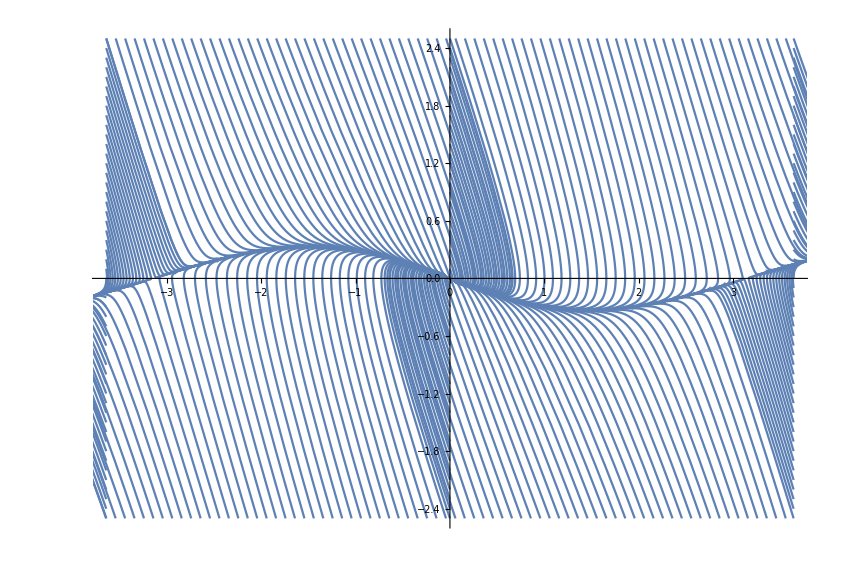

```mathematica
σ=3;
sol[x0_,y0_]:=NDSolve[{x'[t]==y[t],y'[t]==-Sin[x[t]]-σ*y[t],x[0]==x0,y[0]==y0},{x,y},{t,0,10}]
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. sol[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.03, 0.}],Arrow[x]}]
```

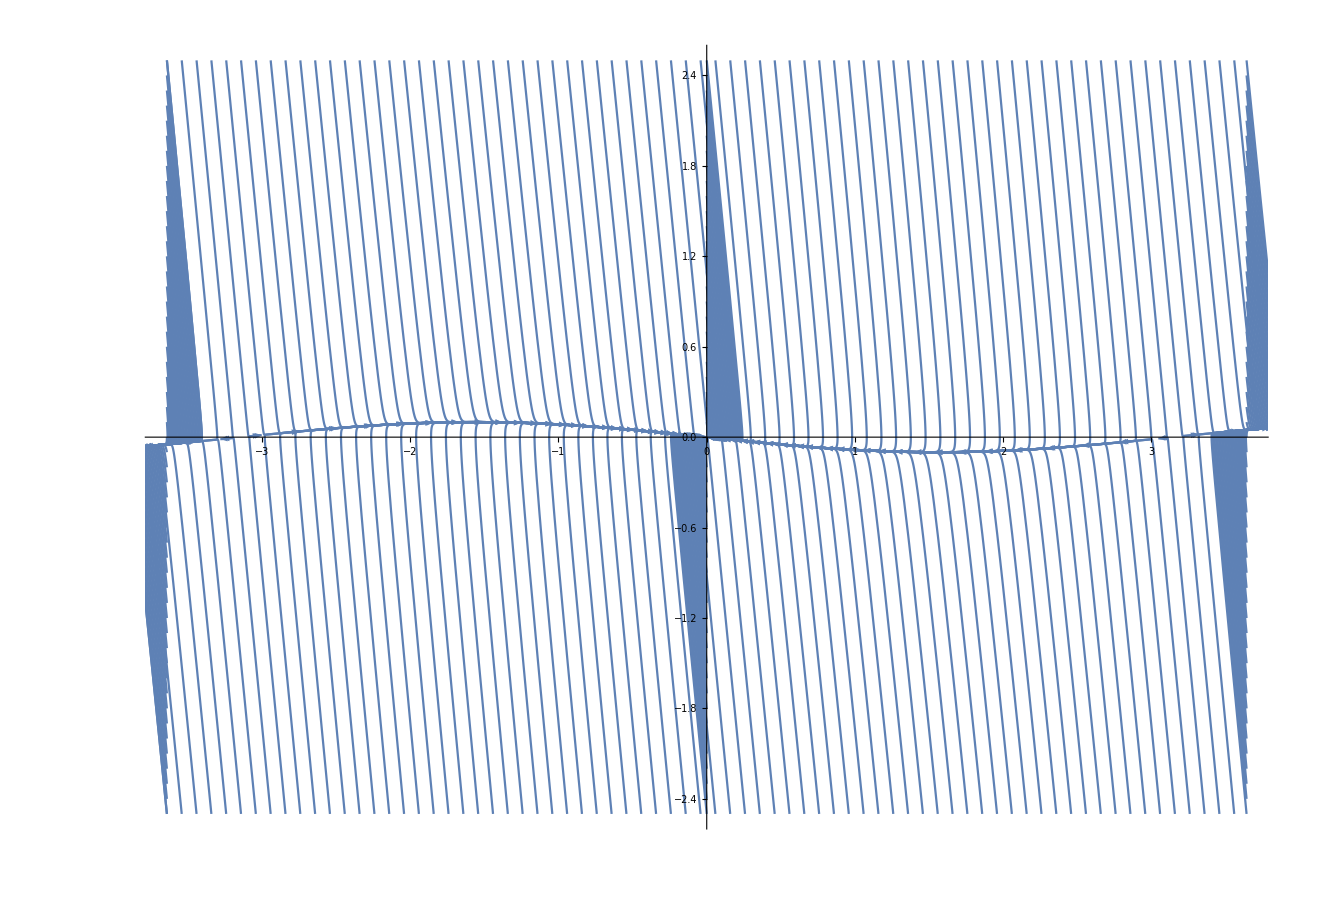

```mathematica
σ=10;
sol[x0_,y0_]:=NDSolve[{x'[t]==y[t],y'[t]==-Sin[x[t]]-σ*y[t],x[0]==x0,y[0]==y0},{x,y},{t,0,10}]
initialCondition=Join[Table[{0,y},{y,miny,maxy,0.1}],Table[{minx,y},{y,miny,maxy,0.1}],Table[{maxx,y},{y,miny,maxy,0.1}],Table[{x,miny},{x,minx,maxx,0.1}],Table[{x,maxy},{x,minx,maxx,0.1}]];
Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/. sol[initialCondition[[i,1]],initialCondition[[i,2]]]],{t,0,10},PlotRange->{{minx,maxx},{miny,maxy}}],{i,Length[initialCondition]}]/. Line[x_]:>{Arrowheads[{0.,0.02, 0.}],Arrow[x]}]
```